```mathematica
<<mf25.m
```

```mathematica
cRaleigh2[α_,β_,ν_]:=Module[{answer,pchhmrA,pchhmrB},
pchhmrA=Pochhammer[α,ν];
pchhmrB=Pochhammer[β,ν];
answer=pchhmrA*pchhmrB/(ν!)^2;
Return[answer]]
```

```mathematica
eRaleigh[α_,β_,ν_]:=Sum[1/(α+p)+1/(β+p)-2/(1+p),{p,0,ν-1}]
```

```mathematica
Fraleigh2[α_,β_,u_,terms_]:=Sum[cRaleigh2[α,β,ν]*u^ν,{ν,0,terms}]
```

```mathematica
FstarRaleigh2[α_,β_,u_,terms_]:=
Module[{ν,fsr},
fsr=Sum[cRaleigh2[α,β,ν]*eRaleigh[α,β,ν]*u^ν,{ν,1,terms}];
Return[fsr]]
```

```mathematica
FstarRaleigh3[n_,m_,x_]:=
Module[{α,β,fsr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fsr2=FstarRaleigh2[α,β,x,n];
fsr2=Series[fsr2,{x,0,n}];
Return[fsr2]]
```

```mathematica
Fraleigh4[n_,m_,x_]:=
Module[{α,β,fr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fr2=Fraleigh2[α,β,x,n];
fr2=Series[fr2,{x,0,n}];
Return[fr2]]
```

```mathematica
exNo3[n_,m_,J_]:=
Module[{a1,a2,a3,a4},
a1=J*Exp[FstarRaleigh3[n,m,J]/Fraleigh4[n,m,J]];
a2=Series[a1,{J,0,n}];
a3=Collect[Normal[a2],J];
a4=Series[a3,{J,0,n}];
Return[a4]]
```

```mathematica
J[n_,m_]:=1/InverseSeries[exNo3[n,m,x],x]
```

```mathematica
deltaInfty[n_,m_]:=
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m];
djay=x*D[jay,x];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^(2*m);
denominator=jay^(2*m-2)*(jay-1)^m;
answer=Collect[Series[(numerator/denominator)^(1/(m-2)),{x,0,n}],x];
Return[Refine[answer,x>0]]]
```

```mathematica
deltaInftyStrike[n_,m_]:=
Module[{f},
f=deltaInfty[n,m]/.x->(2^6*m^3*x);
f=Collect[f,x];
c1=Coefficient[f,x,1];
f=Expand[f/c1];
Return[f]]
```

```mathematica
For[m=2,m<6,m++;
Print["-----------------------------------------------------"];
Print[{m,deltaInfty[7,m]}];
Print[];
Print[{m,deltaInftyStrike[7,m]}];
Print[]]
```

-----------------------------------------------------

{3,x-x^2/72+(7 x^3)/82944-(23 x^4)/80621568+(805 x^5)/1486016741376-(7 x^6)/17832200896512-(2093 x^7)/3327916660110655488}

{3,x-24 x^2+252 x^3-1472 x^4+4830 x^5-6048 x^6-16744 x^7}

-----------------------------------------------------

{4,x-x^2/32+(3 x^3)/16384+x^4/262144-(105 x^5)/2147483648-(3 x^6)/34359738368+(127 x^7)/35184372088832}

{4,x-128 x^2+3072 x^3+262144 x^4-13762560 x^5-100663296 x^6+17045651456 x^7}

-----------------------------------------------------

{5,x-(9 x^2)/200+(279 x^3)/640000+(961 x^4)/192000000-(9633 x^5)/3276800000000-(100656411 x^6)/40960000000000000+(29685769799 x^7)/2359296000000000000000}

{5,x-360 x^2+27900 x^3+(7688000 x^4)/3-12041250 x^5-80525128800 x^6+(29685769799000 x^7)/9}

-----------------------------------------------------

{6,x-x^2/18+x^3/1296+x^4/314928+x^5/22674816-x^6/272097792-(5 x^7)/198359290368}

{6,x-768 x^2+147456 x^3+8388608 x^4+1610612736 x^5-1855425871872 x^6-175921860444160 x^7}

```mathematica
fi=Collect[deltaInftyStrike[25,3],x];
ex=Exponent[fi,x];
no=0;
For[n=0,n<ex,n++;
cf=Coefficient[fi,x,n];
If[cf≠RamanujanTau[n],no++]];
Print[no]
```

0

```mathematica
stream=OpenWrite["run17aug21no50"];
For[m=2,m<153,m++;
fi=deltaInftyStrike[50,m];
Write[stream,{m,Collect[fi,x]}]];
Close[stream]
```

PiecewiseExpand::mpwc: PiecewiseExpand was unable to convert Floor[1/2-(50 Arg[x])/π] to Piecewise because the required number 101 of piecewise cases sought exceeds the internal limit $MaxPiecewiseCases = 100.

General::stop: Further output of PiecewiseExpand::mpwc will be suppressed during this calculation.

run17aug21no50

```mathematica
stream=OpenRead["run17aug21no50"];
list=ReadList[stream];
Close[stream];
m=Last[list][[1]];
xp=Exponent[Last[list][[2]],x];
Print[{Length[list],m,xp}]
```

{151,153,50}

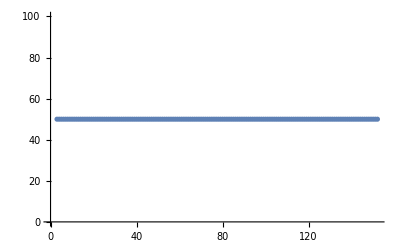

```mathematica
stream=OpenRead["run17aug21no50"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<150,k++;
n=list[[k]][[1]];
poly=list[[k]][[2]];
xp=Exponent[poly,x];
AppendTo[data,{n,xp}]];
Print[ListPlot[data]]
```

```mathematica
stream=OpenRead["run17aug21no50"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<150,k++;
n=list[[k]][[1]];
poly=list[[k]][[2]];
cf=Coefficient[poly,x,0];
AppendTo[data,{n,cf}]];
Print[data]
```

{{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},{79,0},{80,0},{81,0},{82,0},{83,0},{84,0},{85,0},{86,0},{87,0},{88,0},{89,0},{90,0},{91,0},{92,0},{93,0},{94,0},{95,0},{96,0},{97,0},{98,0},{99,0},{100,0},{101,0},{102,0},{103,0},{104,0},{105,0},{106,0},{107,0},{108,0},{109,0},{110,0},{111,0},{112,0},{113,0},{114,0},{115,0},{116,0},{117,0},{118,0},{119,0},{120,0},{121,0},{122,0},{123,0},{124,0},{125,0},{126,0},{127,0},{128,0},{129,0},{130,0},{131,0},{132,0},{133,0},{134,0},{135,0},{136,0},{137,0},{138,0},{139,0},{140,0},{141,0},{142,0},{143,0},{144,0},{145,0},{146,0},{147,0},{148,0},{149,0},{150,0},{151,0},{152,0}}

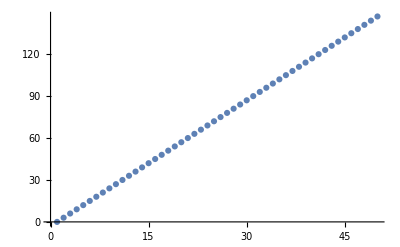

run17aug21no51

```mathematica
stream=OpenRead["run17aug21no50"];
list=ReadList[stream];
Close[stream];
wstream=OpenWrite["run17aug21no51"]; 
degrees={};
For[n=0,n<50,n++;
data={};
For[k=0,k<150,k++;
m=list[[k,1]];
poly=list[[k,2]];
cf=Coefficient[poly,x,n];
AppendTo[data,{m,cf}]
]; (* k *)
ip=InterpolatingPolynomial[data,x];
Write[wstream,{n,ip}];
AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Close[wstream]
```

```mathematica
stream=OpenRead["run17aug21no51"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

50

```mathematica
stream=OpenRead["run17aug21no51"];
list=ReadList[stream];
Close[stream];
For[k=0,k<5,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
poly=factorIntoIrreducibleMonics[poly];
Print[{k,n,poly}]]
```

{1,1,{{1,1},{1,1}}}

{2,2,{{-8,1},{1,1},{-2+x,2},{x,1}}}

{3,3,{{28,1},{1,1},{-2+x,2},{x,2},{76/7-(44 x)/7+x^2,1}}}

{4,4,{{-64,1},{1,1},{1,-1},{-2+x,2},{x,3},{5264/27-(5200 x)/27+(2096 x^2)/27-(44 x^3)/3+x^4,1}}}

{5,5,{{126,1},{1,1},{1,-1},{-2+x,2},{x,4},{7226176/1701-(3141440 x)/567+(5611696 x^2)/1701-(629344 x^3)/567+(364300 x^4)/1701-(4220 x^5)/189+x^6,1}}}

```mathematica
stream=OpenRead["run17aug21no51"];
list=ReadList[stream];
Close[stream];
no={};
For[k=0,k<50,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
divideby=(x-2)^2*x^(n-1);
pr=PolynomialRemainder[poly,divideby,x];
If[pr!=0,no=AppendTo[no,n]]];
Print[no]
```

{1}

```mathematica
stream=OpenRead["run17aug21no51"];
list=ReadList[stream];
Close[stream];
data={};
data2={};
For[k=2,k<50,k++;
n=list[[k,1]];
poly=list[[k,2]];
xp=Exponent[poly,x];
data=AppendTo[data,{n,xp}];
divideby=(x-2)^2*x^(n-1);
poly=PolynomialQuotient[poly,divideby,x];
xp=Exponent[poly,x];
data2=AppendTo[data2,{n,xp}]
];
Print[data];Print[data2]
```

{{3,6},{4,9},{5,12},{6,15},{7,18},{8,21},{9,24},{10,27},{11,30},{12,33},{13,36},{14,39},{15,42},{16,45},{17,48},{18,51},{19,54},{20,57},{21,60},{22,63},{23,66},{24,69},{25,72},{26,75},{27,78},{28,81},{29,84},{30,87},{31,90},{32,93},{33,96},{34,99},{35,102},{36,105},{37,108},{38,111},{39,114},{40,117},{41,120},{42,123},{43,126},{44,129},{45,132},{46,135},{47,138},{48,141},{49,144},{50,147}}

{{3,2},{4,4},{5,6},{6,8},{7,10},{8,12},{9,14},{10,16},{11,18},{12,20},{13,22},{14,24},{15,26},{16,28},{17,30},{18,32},{19,34},{20,36},{21,38},{22,40},{23,42},{24,44},{25,46},{26,48},{27,50},{28,52},{29,54},{30,56},{31,58},{32,60},{33,62},{34,64},{35,66},{36,68},{37,70},{38,72},{39,74},{40,76},{41,78},{42,80},{43,82},{44,84},{45,86},{46,88},{47,90},{48,92},{49,94},{50,96}}

--------------------------------------------------------------

n:  1

-Graphics-

--------------------------------------------------------------

n:  2

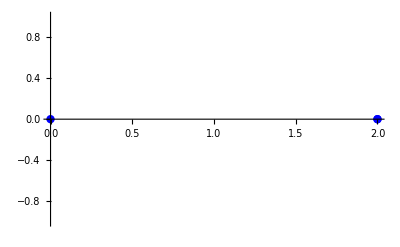

--------------------------------------------------------------

n:  3

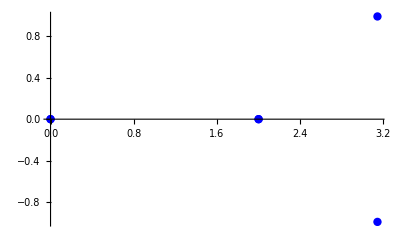

--------------------------------------------------------------

n:  4

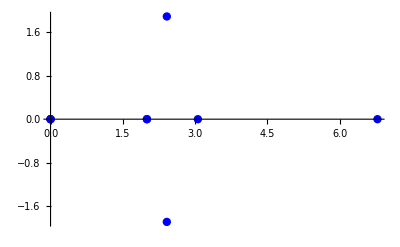

--------------------------------------------------------------

n:  5

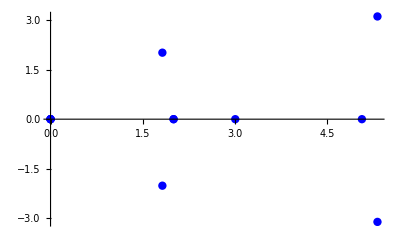

--------------------------------------------------------------

n:  6

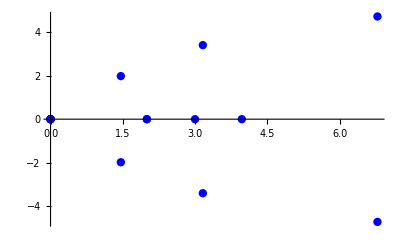

--------------------------------------------------------------

n:  7

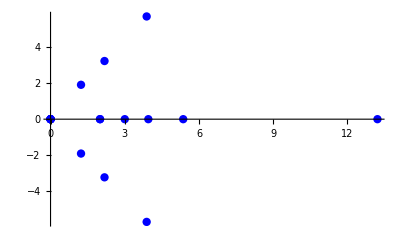

--------------------------------------------------------------

n:  8

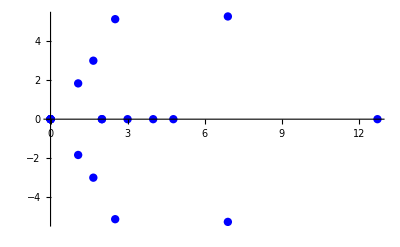

--------------------------------------------------------------

n:  9

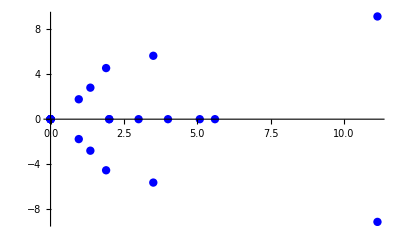

--------------------------------------------------------------

n:  10

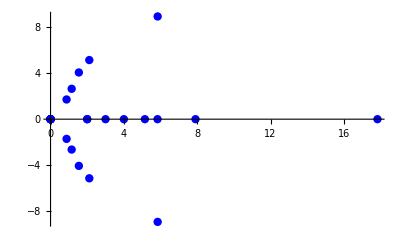

--------------------------------------------------------------

n:  11

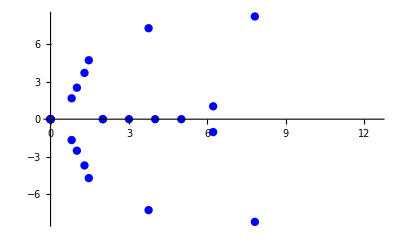

--------------------------------------------------------------

n:  12

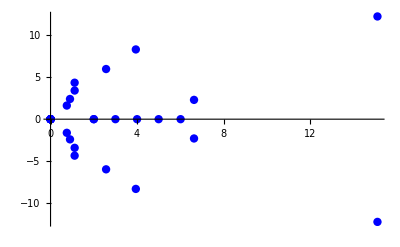

--------------------------------------------------------------

n:  13

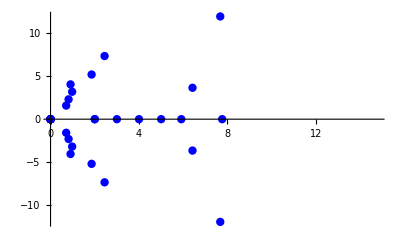

--------------------------------------------------------------

n:  14

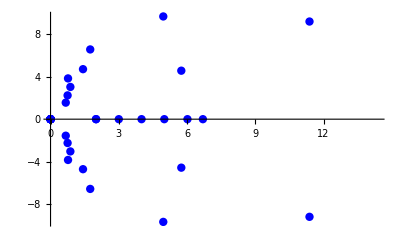

--------------------------------------------------------------

n:  15

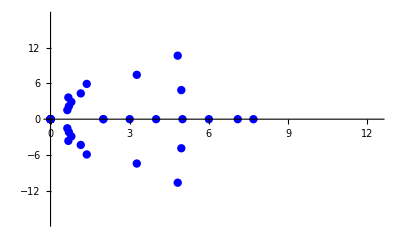

--------------------------------------------------------------

n:  16

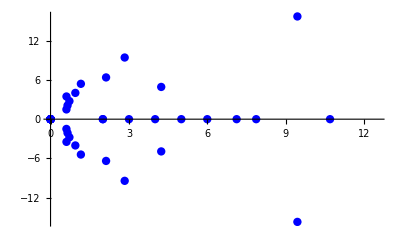

--------------------------------------------------------------

n:  17

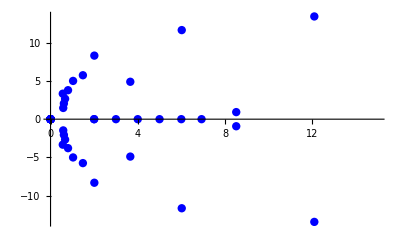

--------------------------------------------------------------

n:  18

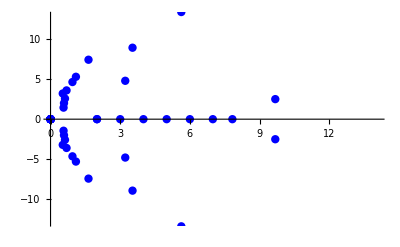

--------------------------------------------------------------

n:  19

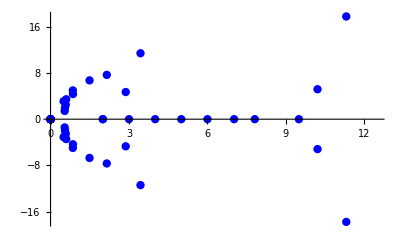

--------------------------------------------------------------

n:  20

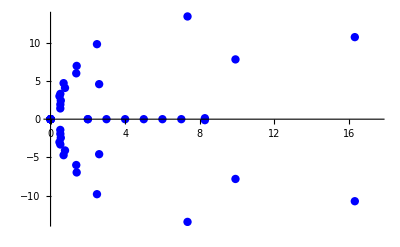

--------------------------------------------------------------

n:  21

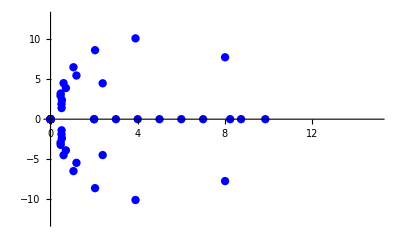

--------------------------------------------------------------

n:  22

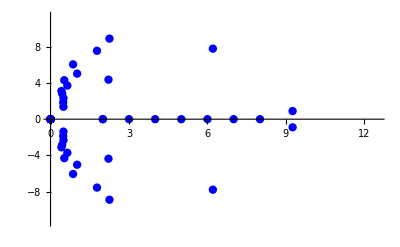

--------------------------------------------------------------

n:  23

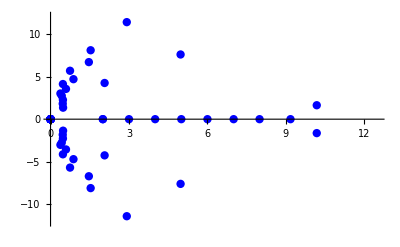

--------------------------------------------------------------

n:  24

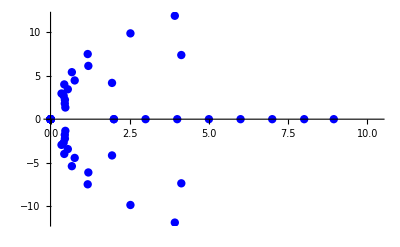

--------------------------------------------------------------

n:  25

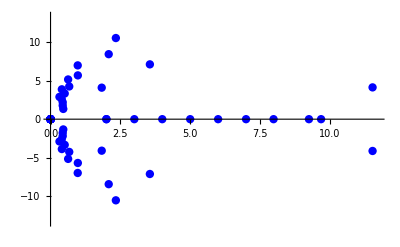

--------------------------------------------------------------

n:  26

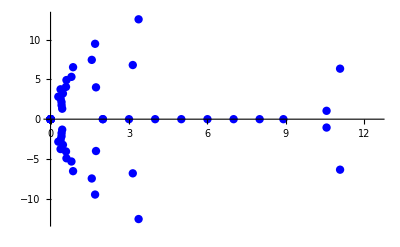

--------------------------------------------------------------

n:  27

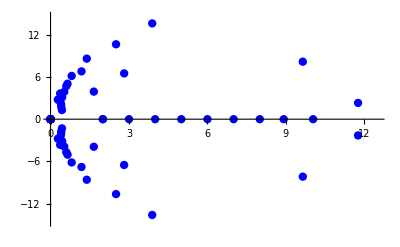

--------------------------------------------------------------

n:  28

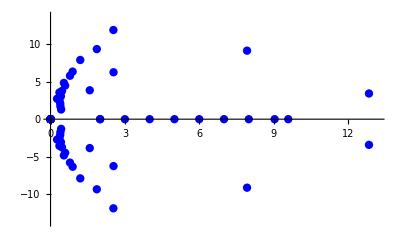

--------------------------------------------------------------

n:  29

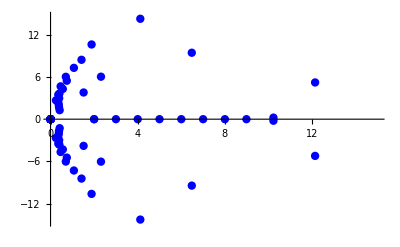

--------------------------------------------------------------

n:  30

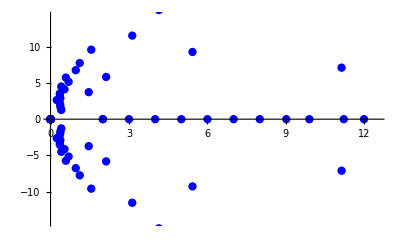

--------------------------------------------------------------

n:  31

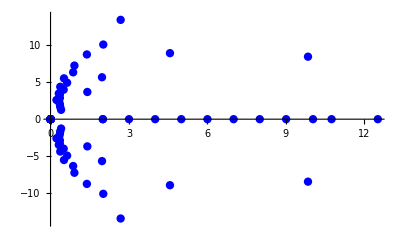

--------------------------------------------------------------

n:  32

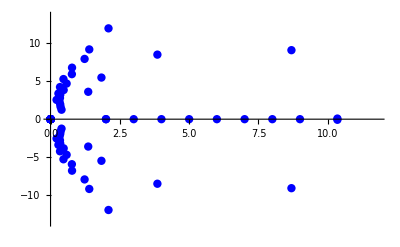

--------------------------------------------------------------

n:  33

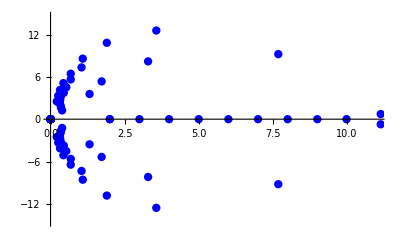

--------------------------------------------------------------

n:  34

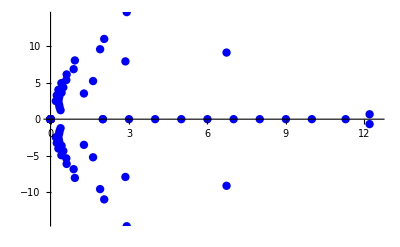

--------------------------------------------------------------

n:  35

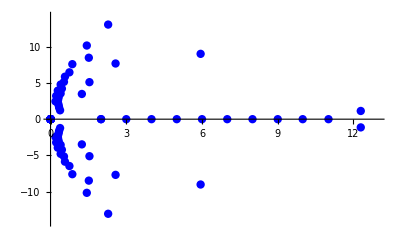

--------------------------------------------------------------

n:  36

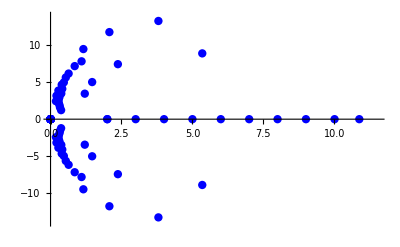

--------------------------------------------------------------

n:  37

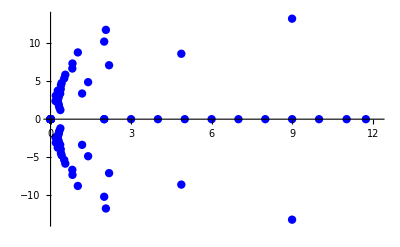

--------------------------------------------------------------

n:  38

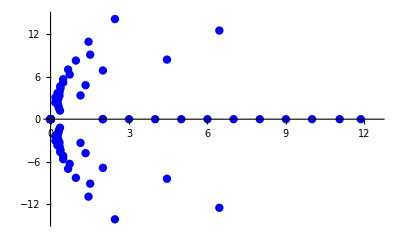

--------------------------------------------------------------

n:  39

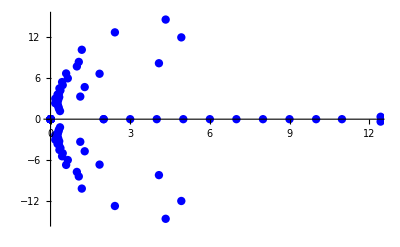

--------------------------------------------------------------

n:  40

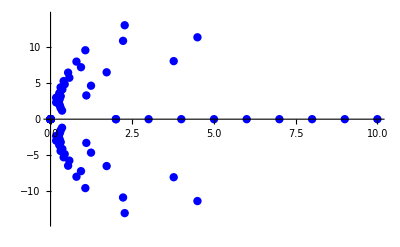

--------------------------------------------------------------

n:  41

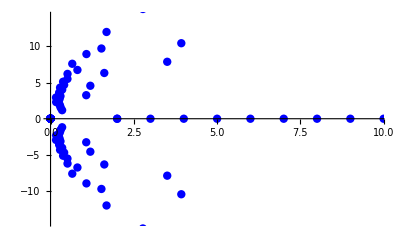

--------------------------------------------------------------

n:  42

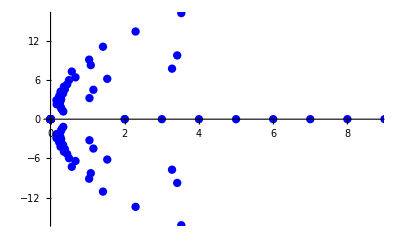

--------------------------------------------------------------

n:  43

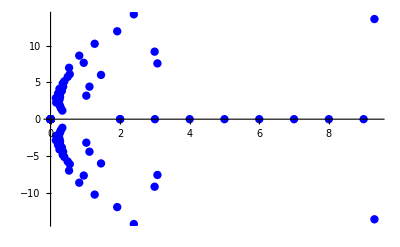

--------------------------------------------------------------

n:  44

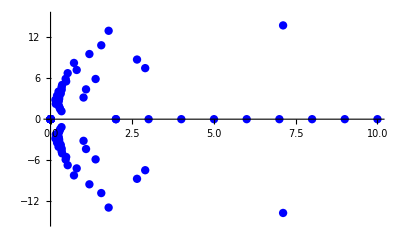

--------------------------------------------------------------

n:  45

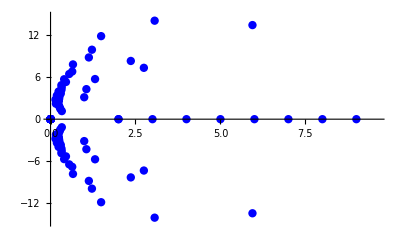

--------------------------------------------------------------

n:  46

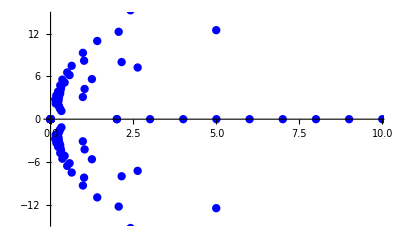

--------------------------------------------------------------

n:  47

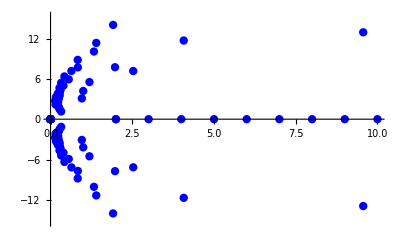

--------------------------------------------------------------

n:  48

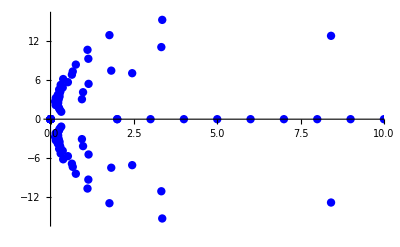

--------------------------------------------------------------

n:  49

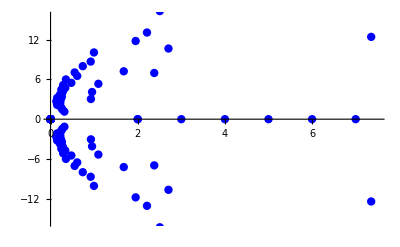

--------------------------------------------------------------

n:  50

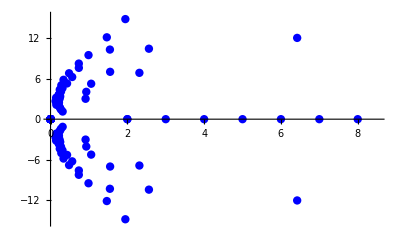

mins

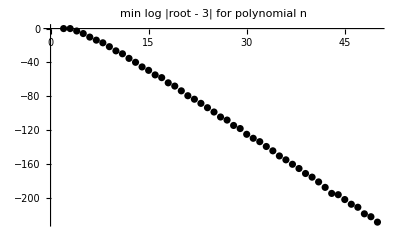

```mathematica
rstream=OpenRead["run17aug21no51"];
list=ReadList[rstream];
Close[rstream];
pointsize=.015;
color=Blue;
mins={};
degrees={};
no=0;
precision=300;
For[k=0,k<50,k++;
Print["--------------------------------------------------------------"];
n=list[[k,1]];
poly=list[[k,2]];
Print["n:  ",n];
plotRoots2[poly,x,pointsize,color];
roots=listRoots3[poly,x,precision];
If[MemberQ[roots,3]==True,no++];
min=Min[Log[Abs[roots-3]]];
AppendTo[mins,{n,min}]
];
Print["mins"];
Print[ListPlot[mins,PlotStyle->Black,PlotLabel->"min log |root - 3| for polynomial n"]]
```

--------------------------------------------------------------

n:  1

-Graphics-

--------------------------------------------------------------

n:  2

-Graphics-

--------------------------------------------------------------

n:  3

-Graphics-

--------------------------------------------------------------

n:  4

-Graphics-

--------------------------------------------------------------

n:  5

-Graphics-

--------------------------------------------------------------

n:  6

-Graphics-

--------------------------------------------------------------

n:  7

-Graphics-

--------------------------------------------------------------

n:  8

-Graphics-

--------------------------------------------------------------

n:  9

-Graphics-

--------------------------------------------------------------

n:  10

-Graphics-

--------------------------------------------------------------

n:  11

-Graphics-

--------------------------------------------------------------

n:  12

-Graphics-

--------------------------------------------------------------

n:  13

-Graphics-

--------------------------------------------------------------

n:  14

-Graphics-

--------------------------------------------------------------

n:  15

-Graphics-

--------------------------------------------------------------

n:  16

-Graphics-

--------------------------------------------------------------

n:  17

-Graphics-

--------------------------------------------------------------

n:  18

-Graphics-

--------------------------------------------------------------

n:  19

-Graphics-

--------------------------------------------------------------

n:  20

-Graphics-

--------------------------------------------------------------

n:  21

-Graphics-

--------------------------------------------------------------

n:  22

-Graphics-

--------------------------------------------------------------

n:  23

-Graphics-

--------------------------------------------------------------

n:  24

-Graphics-

--------------------------------------------------------------

n:  25

-Graphics-

--------------------------------------------------------------

n:  26

-Graphics-

--------------------------------------------------------------

n:  27

-Graphics-

--------------------------------------------------------------

n:  28

-Graphics-

--------------------------------------------------------------

n:  29

-Graphics-

--------------------------------------------------------------

n:  30

-Graphics-

--------------------------------------------------------------

n:  31

-Graphics-

--------------------------------------------------------------

n:  32

-Graphics-

--------------------------------------------------------------

n:  33

-Graphics-

--------------------------------------------------------------

n:  34

-Graphics-

--------------------------------------------------------------

n:  35

-Graphics-

--------------------------------------------------------------

n:  36

-Graphics-

--------------------------------------------------------------

n:  37

-Graphics-

--------------------------------------------------------------

n:  38

-Graphics-

--------------------------------------------------------------

n:  39

-Graphics-

--------------------------------------------------------------

n:  40

-Graphics-

--------------------------------------------------------------

n:  41

-Graphics-

--------------------------------------------------------------

n:  42

-Graphics-

--------------------------------------------------------------

n:  43

-Graphics-

--------------------------------------------------------------

n:  44

-Graphics-

--------------------------------------------------------------

n:  45

-Graphics-

--------------------------------------------------------------

n:  46

-Graphics-

--------------------------------------------------------------

n:  47

-Graphics-

--------------------------------------------------------------

n:  48

-Graphics-

--------------------------------------------------------------

n:  49

-Graphics-

--------------------------------------------------------------

n:  50

-Graphics-

mins

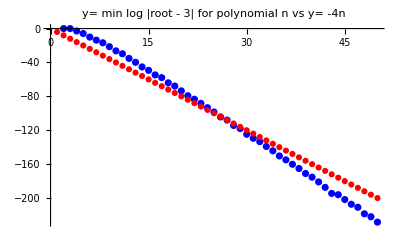

```mathematica
rstream=OpenRead["run17aug21no51"];
list=ReadList[rstream];
Close[rstream];
pointsize=.015;
color=Blue;
mins={};
degrees={};
no=0;
precision=300;
data={};
For[k=0,k<50,k++;
Print["--------------------------------------------------------------"];
n=list[[k,1]];
poly=list[[k,2]];
Print["n:  ",n];
plotRoots2[poly,x,pointsize,color];
roots=listRoots3[poly,x,precision];
If[MemberQ[roots,3]==True,no++];
min=Min[Log[Abs[roots-3]]];
AppendTo[mins,{n,min}];
AppendTo[data,{n,-4*n}]
];
Print["mins"];
lpm=ListPlot[mins,PlotStyle->Blue,PlotLabel->"y= min log |root - 3| for polynomial n vs y= -4n"];
lpd=ListPlot[data,PlotStyle->Red];
Print[Show[lpm,lpd]]
```

```mathematica
rstream=OpenRead["run17aug21no51"];
list=ReadList[rstream];
Close[rstream];
pointsize=.015;
color=Blue;
mins={};
degrees={};
no=0;
precision=300;
data={};
For[k=0,k<50,k++;
Print["--------------------------------------------------------------"];
n=list[[k,1]];
poly=list[[k,2]];
Print["n:  ",n];
plotRoots2[poly,x,pointsize,color];
roots=listRoots3[poly,x,precision];
If[MemberQ[roots,3]==True,no++];
min=Min[Log[Abs[roots-3]]];
AppendTo[mins,{n,min}];
AppendTo[data,{n,-Pi*n}]
];
Print["mins"];
lpm=ListPlot[mins,PlotStyle->Blue,PlotLabel->"y= min log |root - 3| for polynomial n vs y= -π n"];
lpd=ListPlot[data,PlotStyle->Red];
Print[Show[lpm,lpd]]
```

--------------------------------------------------------------

n:  1

-Graphics-

--------------------------------------------------------------

n:  2

-Graphics-

--------------------------------------------------------------

n:  3

-Graphics-

--------------------------------------------------------------

n:  4

-Graphics-

--------------------------------------------------------------

n:  5

-Graphics-

--------------------------------------------------------------

n:  6

-Graphics-

--------------------------------------------------------------

n:  7

-Graphics-

--------------------------------------------------------------

n:  8

-Graphics-

--------------------------------------------------------------

n:  9

-Graphics-

--------------------------------------------------------------

n:  10

-Graphics-

--------------------------------------------------------------

n:  11

-Graphics-

--------------------------------------------------------------

n:  12

-Graphics-

--------------------------------------------------------------

n:  13

-Graphics-

--------------------------------------------------------------

n:  14

-Graphics-

--------------------------------------------------------------

n:  15

-Graphics-

--------------------------------------------------------------

n:  16

-Graphics-

--------------------------------------------------------------

n:  17

-Graphics-

--------------------------------------------------------------

n:  18

-Graphics-

--------------------------------------------------------------

n:  19

-Graphics-

--------------------------------------------------------------

n:  20

-Graphics-

--------------------------------------------------------------

n:  21

-Graphics-

--------------------------------------------------------------

n:  22

-Graphics-

--------------------------------------------------------------

n:  23

-Graphics-

--------------------------------------------------------------

n:  24

-Graphics-

--------------------------------------------------------------

n:  25

-Graphics-

--------------------------------------------------------------

n:  26

-Graphics-

--------------------------------------------------------------

n:  27

-Graphics-

--------------------------------------------------------------

n:  28

-Graphics-

--------------------------------------------------------------

n:  29

-Graphics-

--------------------------------------------------------------

n:  30

-Graphics-

--------------------------------------------------------------

n:  31

-Graphics-

--------------------------------------------------------------

n:  32

-Graphics-

--------------------------------------------------------------

n:  33

-Graphics-

--------------------------------------------------------------

n:  34

-Graphics-

--------------------------------------------------------------

n:  35

-Graphics-

--------------------------------------------------------------

n:  36

-Graphics-

--------------------------------------------------------------

n:  37

-Graphics-

--------------------------------------------------------------

n:  38

-Graphics-

--------------------------------------------------------------

n:  39

-Graphics-

--------------------------------------------------------------

n:  40

-Graphics-

--------------------------------------------------------------

n:  41

-Graphics-

--------------------------------------------------------------

n:  42

-Graphics-

--------------------------------------------------------------

n:  43

-Graphics-

--------------------------------------------------------------

n:  44

-Graphics-

--------------------------------------------------------------

n:  45

-Graphics-

--------------------------------------------------------------

n:  46

-Graphics-

--------------------------------------------------------------

n:  47

-Graphics-

--------------------------------------------------------------

n:  48

-Graphics-

--------------------------------------------------------------

n:  49

-Graphics-

--------------------------------------------------------------

n:  50

-Graphics-

mins

-Graphics-